```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

## Functions that generate lists of integer "clues", and function to ID sessie network

### Explanations

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"1D"|"2D"|...|"exp", n, {k, delay, matchlen, match}, dt}, indicating an n-dimensional or exponential network. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match of length matchlen was detected. The difference table dt is provided for human inspection, but in theory it (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary. The function GuessDimension collects IDs ("1D", "2D", etc.) returned for any of the 4 significant number generator functions, and considers matchlen as a measure of reliability.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if the combined matchlen values returned indicate satisfactory reliability.

#### TestForUnusedRules: decides whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, call TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Later call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss]; (* update it if changed *)
Print[vdct];
ans
];
```

## Done & To Do

Done: 
★ Rewrite CheckDimension to make it more robust and general, add some checks.  Return value tweaked to give more information.  Calls RecognizeDifferenceRow for actual recognition step.
★ Add checks to ReliableDistances, so it doesn't squawk for disconnected 1-d networks.
★ Write loop to compare different versions of ID summaries, print some interesting cases.  Note that different functions do produce different summaries, these are not unique, but should correctly ID the network.
★ Both 1-D loop and 2-D loop are turning up some probable bugs.  Results of investigation:  It's when CheckDimension is handed a list with ≤2 pts.  Solution:  Write a wrapper function that runs checks before passing them to CheckDimension, etc.
★ GuessDimension:  wrapper function runs needed checks, and grows the sessie if needed to reach agreement for CheckDimension as applied to MaxStateLengthPositions, LeastUsedRulePositions, and DistanceLastPositions, DistanceTally.  Assign a dimension to "Verdict" if warranted (≥ 2 tests agree within 5000 steps).
★ Write function TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

To Do:
★ Write function ImproveInitialState to select a better initial state string, based on the sessie/net ID results provided by CheckDimension, and unchanged tags in "TEvolution". 
★ Add a "NetSummary" field to the sessie object?  [Yes!  Once the dimension has been identified.]

★ Order to do things:  
1. GuessDimension:  Sets "Verdict" if justifiable.  ✓
2. TestForUnusedRules:  Checks that "Verdict" has been assigned, are all rules used in intervals provided by MaxStateLengthPositions, LeastUsedRulePositions, and DistanceLastPositions.  Else long-jump.  ✓
3. ImproveInitialState for cases only we care about.
4. Derive and assign canonical value to "NetSummary".  Add to database.

### Function to perform loops

```mathematica
doEnumerate[start_Integer, stop_Integer, lookfor_List, keep_(True|False)] :=
```

### Start of code to summarize Net:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]}];
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

*** Start here: recognize a row of net difference sets, by (?) "subtracting" with various offsets, identifying case with most 0 entries *)

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

```mathematica
SetSubtract[1·{{1,3}},1·{{1,1,1}}]
```

{}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

```mathematica
{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},
2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},
3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}
```

```mathematica
Subtract[10,4]
```

6

```mathematica
With[{l = ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]},
Print[l[[5+8;;-1]]];
Print[l[[1+8;;-5]]];
Print[SetSubtract[l[[5+8;;-1]], l[[1+8;;-5]]]];
 Print[];
Table[SetSubtract[l[[k;;]], l[[;;-k]]], {k, 2, Length[l]/2}]
 ]
```

{1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

{1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}}}

{0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}

{{0·{{0,2,∞}},0·{∞},0·{{0,0,1}},0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,1}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,1}},∞,0·{∞},0·{{0,0,4}},2·{{0,0,1}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,1}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,1}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,1}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,1}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,1}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{2,3,∞}},0·{{0,0,-1}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{{0,0,-3}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},∞,0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{∞}},{0·{{0,0,1}},0·{{2,1}},0·{{0,0,0}},0·{{0,0,1}},0·{∞},0·{{3,4,∞}},0·{{0,0,-2}},0·{{0,0,0}},1·{∞},0·{{4,5,∞}},0·{{0,0,-3}},∞,2·{∞},0·{{5,6,∞}},0·{{0,0,-4}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-5}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-6}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-7}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-8}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-9}},0·{{0,0,∞}}},{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,2}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,2}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,2}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,2}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,2}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,2}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,2}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,2}},0·{∞},0·{{3,4,∞}},0·{{0,0,-1}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{{0,0,-3}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-9,-10}}},{0·{{0,0,3}},0·{{3,2}},0·{{0,0,0}},0·{{0,0,2}},1·{∞},0·{{4,5,∞}},0·{{0,0,-2}},0·{{0,0,1}},2·{∞},0·{{5,6,∞}},0·{{0,0,-3}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-4}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-5}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-6}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-7}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-8}},1·{{0,0,∞}}},{0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,3}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,3}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,3}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,3}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,3}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,3}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,3}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,3}},1·{∞},0·{{4,5,∞}},0·{{0,0,-1}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{{0,0,-3}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-8,-9}}},{1·{{0,0,4}},0·{{4,3}},0·{{0,0,0}},0·{{0,0,3}},2·{∞},0·{{5,6,∞}},0·{{0,0,-2}},0·{{0,0,2}},3·{∞},0·{{6,7,∞}},0·{{0,0,-3}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-4}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-5}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-6}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-7}},2·{{0,0,∞}}},{0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,4}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,4}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,4}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,4}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,4}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,4}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,4}},2·{∞},0·{{5,6,∞}},0·{{0,0,-1}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{{0,0,-3}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-7,-8}}},{2·{{0,0,5}},0·{{5,4}},0·{{0,0,0}},0·{{0,0,4}},3·{∞},0·{{6,7,∞}},0·{{0,0,-2}},0·{{0,0,3}},4·{∞},0·{{7,8,∞}},0·{{0,0,-3}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-4}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-5}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-6}},3·{{0,0,∞}}},{0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,5}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,5}},0·{{7,8,∞}},0·{∞},0·{{0,0,7}},5·{{0,0,5}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,5}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,5}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,5}},3·{∞},0·{{6,7,∞}},0·{{0,0,-1}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},0·{{0,0,-3}},0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-6,-7}}}}

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
SetSubtract[{1,2,3},{1,2,3,5}]
```

{0,0,0,∞}

```mathematica
SetSubtract[{1,2,3},{1,2}]
```

∞

```mathematica
SetSubtract[3·{{1,2,4}},1·{{1,2,3}}]
```

2·{{0,0,1}}

```mathematica
SetSubtract[{1,3,7},{1,2,3}]
```

{0,1,4}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

{{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%377,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

```mathematica
MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1]
```

{{0,1,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,3,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{7,4,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,5,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{6,6,{{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,7,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
Count[{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},_?AtomQ,∞]
```

8

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
}]]
```

{7·{{0},{}},1·{{0}}}

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]]
```

{7·{{0},{}},{0}}

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]] // idMatch
```

{0,7,{{0},{}},1}

```mathematica
RecognizeNet[sss_Association /; KeyExistsQ[sss,"Net"]] := 
Module[{netdiffs=ToNetDifferenceSets[sss["Net"]],
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequencePosition[l,
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]},Overlaps->False
]
]
```

{{1,14}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToNetDifferenceSets[sss1a["Net"]]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

{0,8,{{1},{}},1}

{100%,{2,0,8,{{1},{}},1}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToReducedNetDifferenceSets@ToNetDifferenceSets[sss90["Net"]]
```

{135,4,{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}}

{0,1,{{1,1,1}},38}

{103.846%,{4,0,1,{{1,1,1}},38}}

```mathematica
With[{ptrn={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
MatchQ[ptrn,{Repeated[__,{0,5}],Longest[Repeated[b__,{5,∞}]],Repeated[__,{0,3}]}]
]
```

True

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

Clear[SubtractSetLists];
SubtractSetLists[s1_List, s2_List] := Module[{len1, len2},
   MapThread[If[(len1 = Length[#1]) < (len2 = Length[#2]), ∞, Join[#2 - #1[[1 ;; len2]], Table[∞, len1 - len2]]] &, {s1, s2}]
   ];

With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SubtractSetLists[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]

{{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}

```mathematica
Count[#,0,∞]& /@ %219
```

{0,8,0,7,0,6,0}

#### Code still being tested:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]}];
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

*** Start here: recognize a row of net difference sets, by (?) "subtracting" with various offsets, identifying case with most 0 entries *)

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

```mathematica
SetSubtract[1·{{1,3}},1·{{1,1,1}}]
```

{}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

```mathematica
{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},
2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},
3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}
```

```mathematica
Subtract[10,4]
```

6

```mathematica
With[{l = ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]},
Print[l[[5+8;;-1]]];
Print[l[[1+8;;-5]]];
Print[SetSubtract[l[[5+8;;-1]], l[[1+8;;-5]]]];
 Print[];
Table[SetSubtract[l[[k;;]], l[[;;-k]]], {k, 2, Length[l]/2}]
 ]
```

{1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

{1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}}}

{0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}

{{0·{{0,2,∞}},0·{∞},0·{{0,0,1}},0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,1}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,1}},∞,0·{∞},0·{{0,0,4}},2·{{0,0,1}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,1}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,1}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,1}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,1}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,1}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{2,3,∞}},0·{{0,0,-1}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{{0,0,-3}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},∞,0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{∞}},{0·{{0,0,1}},0·{{2,1}},0·{{0,0,0}},0·{{0,0,1}},0·{∞},0·{{3,4,∞}},0·{{0,0,-2}},0·{{0,0,0}},1·{∞},0·{{4,5,∞}},0·{{0,0,-3}},∞,2·{∞},0·{{5,6,∞}},0·{{0,0,-4}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-5}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-6}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-7}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-8}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-9}},0·{{0,0,∞}}},{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,2}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,2}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,2}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,2}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,2}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,2}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,2}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,2}},0·{∞},0·{{3,4,∞}},0·{{0,0,-1}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{{0,0,-3}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-9,-10}}},{0·{{0,0,3}},0·{{3,2}},0·{{0,0,0}},0·{{0,0,2}},1·{∞},0·{{4,5,∞}},0·{{0,0,-2}},0·{{0,0,1}},2·{∞},0·{{5,6,∞}},0·{{0,0,-3}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-4}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-5}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-6}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-7}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-8}},1·{{0,0,∞}}},{0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,3}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,3}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,3}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,3}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,3}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,3}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,3}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,3}},1·{∞},0·{{4,5,∞}},0·{{0,0,-1}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{{0,0,-3}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-8,-9}}},{1·{{0,0,4}},0·{{4,3}},0·{{0,0,0}},0·{{0,0,3}},2·{∞},0·{{5,6,∞}},0·{{0,0,-2}},0·{{0,0,2}},3·{∞},0·{{6,7,∞}},0·{{0,0,-3}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-4}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-5}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-6}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-7}},2·{{0,0,∞}}},{0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,4}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,4}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,4}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,4}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,4}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,4}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,4}},2·{∞},0·{{5,6,∞}},0·{{0,0,-1}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{{0,0,-3}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-7,-8}}},{2·{{0,0,5}},0·{{5,4}},0·{{0,0,0}},0·{{0,0,4}},3·{∞},0·{{6,7,∞}},0·{{0,0,-2}},0·{{0,0,3}},4·{∞},0·{{7,8,∞}},0·{{0,0,-3}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-4}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-5}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-6}},3·{{0,0,∞}}},{0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,5}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,5}},0·{{7,8,∞}},0·{∞},0·{{0,0,7}},5·{{0,0,5}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,5}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,5}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,5}},3·{∞},0·{{6,7,∞}},0·{{0,0,-1}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},0·{{0,0,-3}},0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-6,-7}}}}

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
SetSubtract[{1,2,3},{1,2,3,5}]
```

{0,0,0,∞}

```mathematica
SetSubtract[{1,2,3},{1,2}]
```

∞

```mathematica
SetSubtract[3·{{1,2,4}},1·{{1,2,3}}]
```

2·{{0,0,1}}

```mathematica
SetSubtract[{1,3,7},{1,2,3}]
```

{0,1,4}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

{{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%377,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

```mathematica
MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1]
```

{{0,1,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,3,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{7,4,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,5,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{6,6,{{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,7,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
Count[{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},_?AtomQ,∞]
```

8

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
}]]
```

{7·{{0},{}},1·{{0}}}

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]]
```

{7·{{0},{}},{0}}

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]] // idMatch
```

{0,7,{{0},{}},1}

```mathematica
RecognizeNet[sss_Association /; KeyExistsQ[sss,"Net"]] := 
Module[{netdiffs=ToNetDifferenceSets[sss["Net"]],
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequencePosition[l,
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]},Overlaps->False
]
]
```

{{1,14}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToNetDifferenceSets[sss1a["Net"]]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

{0,8,{{1},{}},1}

{100%,{2,0,8,{{1},{}},1}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToReducedNetDifferenceSets@ToNetDifferenceSets[sss90["Net"]]
```

{135,4,{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}}

{0,1,{{1,1,1}},38}

{103.846%,{4,0,1,{{1,1,1}},38}}

```mathematica
With[{ptrn={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
MatchQ[ptrn,{Repeated[__,{0,5}],Longest[Repeated[b__,{5,∞}]],Repeated[__,{0,3}]}]
]
```

True

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

Clear[SubtractSetLists];
SubtractSetLists[s1_List, s2_List] := Module[{len1, len2},
   MapThread[If[(len1 = Length[#1]) < (len2 = Length[#2]), ∞, Join[#2 - #1[[1 ;; len2]], Table[∞, len1 - len2]]] &, {s1, s2}]
   ];

With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SubtractSetLists[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]

{{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}

```mathematica
Count[#,0,∞]& /@ %219
```

{0,8,0,7,0,6,0}

```mathematica
Clear[TestForUnusedRules];
SetAttributes[TestForUnusedRules,HoldFirst];
TestForUnusedRules[sss0_] := Module[{sss,vdct,ru,rs,evol,testresults,summaries,startpos,unjns,reliableQ,rsobj,ndx,qcode,lastruleused,tailweight,newqcode},
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Verdict"],Return["Invalid input"]];

If[(vdct=sss["Verdict"])=="OK",
GuessDimension[sss]; (* try again *)
If[Length[ru]≠Length[sss["RulesUsed"]], (* changed *) sss0=sss];
If[(vdct=sss["Verdict"])=="OK" ,Return[{}]] (* give up -- can't use this test until we have a "Verdict" *)
];
ru=sss["RulesUsed"]; rs=sss["RuleSet"]; evol=sss["Evolution"];
If[vdct=="Repeating",
startpos=(Position[evol,Last[evol],{1}])⟦-2,1⟧;
ru=ru⟦startpos;;⟧;
If[$debug,Print["Repeating; {start,rules}: ",{startpos,ru}]];
If[Length[Union[ru]]==Length[rs],Return[{}]]; (* all rules used *)
lastruleused = Max[ru], (* find last rule used in Repeating case *)
(* else some other verdict has been assigned *)
testresults=Select[{MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss]},Length[#]≥6&];
If[$debug,Print["testresults: ", testresults]];
summaries=CheckDimension /@ testresults;
If[$debug,Print["summaries: ",summaries]];
startpos=Length[#⟦3,1,1,1⟧]& /@ summaries;
If[$debug,Print["startpos: ",startpos]];
If[$debug,Print["intervals to check for rule usage: ",
MapThread[Partition[#1⟦#2;;⟧,2,1]&,{testresults,startpos}] ]];
If[$debug,Print["rules used in intervals: ",
Map[Part[ru,Span@@#]& ,
MapThread[Partition[#1⟦#2;;⟧,2,1]&,{testresults,startpos}] ,
{2}]]];
unjns=Map[Union[Part[ru,Span@@#]]& ,
MapThread[Partition[#1⟦#2;;⟧,2,1]&,{testresults,startpos}] ,
{2}];
If[$debug,Print["unions of the list of rules used in the intervals: ",unjns]];
reliableQ=(Length[#]>If[vdct=="Repeating",4,8] && Length[Union[#]]==1)&[Flatten[unjns,1]];
If[$debug,Print["reliableQ: ",reliableQ]];
If[!reliableQ,Print["unreliable case: ", rs,": ",summaries]; Return[{}]];
If[$debug,Print["comparing: ",Length[unjns⟦1,1⟧]," to ",Length[rs]]];
If[Length[unjns⟦1,1⟧]==Length[rs],Return[{}]]; (* all rules used *)
lastruleused = Max[unjns⟦1,1⟧]   (* find last rule used in other cases *)
];
tailweight=RuleSetWeight[rs⟦lastruleused+1;;⟧];
If[$debug,Print["lastruleused, tailweight: ",{lastruleused,tailweight}]];
rsobj =FromReducedRankRuleSet[rs];
ndx=rsobj["Index"]; qcode=rsobj["QCode"];
If[tailweight==0,Return[FromReducedRankIndex[ndx+1]]]; (* skip one, go on *)
newqcode= StringDrop[qcode,-tailweight]<>"3"<>(StringJoin@@Table["0",{tailweight-1}]);
Return[FromReducedRankQuinaryCode[newqcode]] 
];
```

## Other stuff...

### Musing on order of things to try: differences, partitioning, totals:

#### Constructed example where table of simple differences fails:

```mathematica
input=Flatten@Table[{n^3-5 n^2+2 n+28,2 n^3+n^2-3 n+18},{n,1,8}];
FixedPointList[Differences,input]//Column
```

{26,44,64,96,112,184,204,354,392,670,746,1214,1354,2086,2322,3404}
{18,20,32,16,72,20,150,38,278,76,468,140,732,236,1082}
{2,12,-16,56,-52,130,-112,240,-202,392,-328,592,-496,846}
{10,-28,72,-108,182,-242,352,-442,594,-720,920,-1088,1342}
{-38,100,-180,290,-424,594,-794,1036,-1314,1640,-2008,2430}
{138,-280,470,-714,1018,-1388,1830,-2350,2954,-3648,4438}
{-418,750,-1184,1732,-2406,3218,-4180,5304,-6602,8086}
{1168,-1934,2916,-4138,5624,-7398,9484,-11906,14688}
{-3102,4850,-7054,9762,-13022,16882,-21390,26594}
{7952,-11904,16816,-22784,29904,-38272,47984}
{-19856,28720,-39600,52688,-68176,86256}
{48576,-68320,92288,-120864,154432}
{-116896,160608,-213152,275296}
{277504,-373760,488448}
{-651264,862208}
{1513472}
{}
{}

```mathematica
CheckDimension[input]
```

{failed,26 | 44 | 64 | 96 | 112 | 184 | 204 | 354 | 392 | 670 | 746 | 1214 | 1354 | 2086 | 2322 | 3404
18 | 20 | 32 | 16 | 72 | 20 | 150 | 38 | 278 | 76 | 468 | 140 | 732 | 236 | 1082 | 
2 | 12 | -16 | 56 | -52 | 130 | -112 | 240 | -202 | 392 | -328 | 592 | -496 | 846 |  | 
10 | -28 | 72 | -108 | 182 | -242 | 352 | -442 | 594 | -720 | 920 | -1088 | 1342 |  |  | 
-38 | 100 | -180 | 290 | -424 | 594 | -794 | 1036 | -1314 | 1640 | -2008 | 2430 |  |  |  | 
138 | -280 | 470 | -714 | 1018 | -1388 | 1830 | -2350 | 2954 | -3648 | 4438 |  |  |  |  | 
-418 | 750 | -1184 | 1732 | -2406 | 3218 | -4180 | 5304 | -6602 | 8086 |  |  |  |  |  | 
1168 | -1934 | 2916 | -4138 | 5624 | -7398 | 9484 | -11906 | 14688 |  |  |  |  |  |  | 
-3102 | 4850 | -7054 | 9762 | -13022 | 16882 | -21390 | 26594 |  |  |  |  |  |  |  | 
7952 | -11904 | 16816 | -22784 | 29904 | -38272 | 47984 |  |  |  |  |  |  |  |  | 
-19856 | 28720 | -39600 | 52688 | -68176 | 86256 |  |  |  |  |  |  |  |  |  | 
48576 | -68320 | 92288 | -120864 | 154432 |  |  |  |  |  |  |  |  |  |  | 
-116896 | 160608 | -213152 | 275296 |  |  |  |  |  |  |  |  |  |  |  | }

### Try partitioning, then making the table of differences. Works for this constructed case, might not work as well in the wild:

```mathematica
FixedPointList[Differences,Partition[input,2]]//Column
```

{{26,18},{20,32},{16,72},{20,150},{38,278},{76,468},{140,732},{236,1082}}
{{-6,14},{-4,40},{4,78},{18,128},{38,190},{64,264},{96,350}}
{{2,26},{8,38},{14,50},{20,62},{26,74},{32,86}}
{{6,12},{6,12},{6,12},{6,12},{6,12}}
{{0,0},{0,0},{0,0},{0,0}}
{{0,0},{0,0},{0,0}}
{{0,0},{0,0}}
{{0,0}}
{}
{}

### Try partitioning & totalling first, then create table of differences. (Might smooth out natural fluctuations? Easier to recognize a constant row, or a 0 row.)

```mathematica
FixedPointList[Differences,Total/@Partition[input,2]]//Column
```

{44,52,88,170,316,544,872,1318}
{8,36,82,146,228,328,446}
{28,46,64,82,100,118}
{18,18,18,18,18}
{0,0,0,0}
{0,0,0}
{0,0}
{0}
{}
{}

### Try different totaled partitions of each row of the table of differences. Nope, no pattern this way!

```mathematica
input
```

{26,18,20,32,16,72,20,150,38,278,76,468,140,732,236,1082}

```mathematica
AllPartitions[l_List] := {l,Grid[Total /@ Partition[l,#]& /@ Range[1,Length[l]/2]]};
```

```mathematica
AllPartitions[input]
```

{{26,18,20,32,16,72,20,150,38,278,76,468,140,732,236,1082},26 | 18 | 20 | 32 | 16 | 72 | 20 | 150 | 38 | 278 | 76 | 468 | 140 | 732 | 236 | 1082
44 | 52 | 88 | 170 | 316 | 544 | 872 | 1318 |  |  |  |  |  |  |  | 
64 | 120 | 208 | 822 | 1108 |  |  |  |  |  |  |  |  |  |  | 
96 | 258 | 860 | 2190 |  |  |  |  |  |  |  |  |  |  |  | 
112 | 558 | 1652 |  |  |  |  |  |  |  |  |  |  |  |  | 
184 | 1030 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
204 | 1882 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
354 | 3050 |  |  |  |  |  |  |  |  |  |  |  |  |  | }

```mathematica
FixedPointList[AllPartitions[Differences[First[#]]]&, AllPartitions[input]]//Column
```

{{26,18,20,32,16,72,20,150,38,278,76,468,140,732,236,1082},26 | 18 | 20 | 32 | 16 | 72 | 20 | 150 | 38 | 278 | 76 | 468 | 140 | 732 | 236 | 1082
44 | 52 | 88 | 170 | 316 | 544 | 872 | 1318 |  |  |  |  |  |  |  | 
64 | 120 | 208 | 822 | 1108 |  |  |  |  |  |  |  |  |  |  | 
96 | 258 | 860 | 2190 |  |  |  |  |  |  |  |  |  |  |  | 
112 | 558 | 1652 |  |  |  |  |  |  |  |  |  |  |  |  | 
184 | 1030 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
204 | 1882 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
354 | 3050 |  |  |  |  |  |  |  |  |  |  |  |  |  | }
{{-8,2,12,-16,56,-52,130,-112,240,-202,392,-328,592,-496,846},-8 | 2 | 12 | -16 | 56 | -52 | 130 | -112 | 240 | -202 | 392 | -328 | 592 | -496 | 846
-6 | -4 | 4 | 18 | 38 | 64 | 96 |  |  |  |  |  |  |  | 
6 | -12 | 258 | -138 | 942 |  |  |  |  |  |  |  |  |  | 
-10 | 22 | 102 |  |  |  |  |  |  |  |  |  |  |  | 
46 | 4 | 1006 |  |  |  |  |  |  |  |  |  |  |  | 
-6 | 120 |  |  |  |  |  |  |  |  |  |  |  |  | 
124 | 86 |  |  |  |  |  |  |  |  |  |  |  |  | }
{{10,10,-28,72,-108,182,-242,352,-442,594,-720,920,-1088,1342},10 | 10 | -28 | 72 | -108 | 182 | -242 | 352 | -442 | 594 | -720 | 920 | -1088 | 1342
20 | 44 | 74 | 110 | 152 | 200 | 254 |  |  |  |  |  |  | 
-8 | 146 | -332 | 794 |  |  |  |  |  |  |  |  |  | 
64 | 184 | 352 |  |  |  |  |  |  |  |  |  |  | 
-44 | 444 |  |  |  |  |  |  |  |  |  |  |  | 
138 | 462 |  |  |  |  |  |  |  |  |  |  |  | 
-104 | 958 |  |  |  |  |  |  |  |  |  |  |  | }
{{0,-38,100,-180,290,-424,594,-794,1036,-1314,1640,-2008,2430},0 | -38 | 100 | -180 | 290 | -424 | 594 | -794 | 1036 | -1314 | 1640 | -2008 | 2430
-38 | -80 | -134 | -200 | -278 | -368 |  |  |  |  |  |  | 
62 | -314 | 836 | -1682 |  |  |  |  |  |  |  |  | 
-118 | -334 | -646 |  |  |  |  |  |  |  |  |  | 
172 | -902 |  |  |  |  |  |  |  |  |  |  | 
-252 | -846 |  |  |  |  |  |  |  |  |  |  | }
{{-38,138,-280,470,-714,1018,-1388,1830,-2350,2954,-3648,4438},-38 | 138 | -280 | 470 | -714 | 1018 | -1388 | 1830 | -2350 | 2954 | -3648 | 4438
100 | 190 | 304 | 442 | 604 | 790 |  |  |  |  |  | 
-180 | 774 | -1908 | 3744 |  |  |  |  |  |  |  | 
290 | 746 | 1394 |  |  |  |  |  |  |  |  | 
-424 | 2064 |  |  |  |  |  |  |  |  |  | 
594 | 1836 |  |  |  |  |  |  |  |  |  | }
{{176,-418,750,-1184,1732,-2406,3218,-4180,5304,-6602,8086},176 | -418 | 750 | -1184 | 1732 | -2406 | 3218 | -4180 | 5304 | -6602 | 8086
-242 | -434 | -674 | -962 | -1298 |  |  |  |  |  | 
508 | -1858 | 4342 |  |  |  |  |  |  |  | 
-676 | -1636 |  |  |  |  |  |  |  |  | 
1056 | -4666 |  |  |  |  |  |  |  |  | }
{{-594,1168,-1934,2916,-4138,5624,-7398,9484,-11906,14688},-594 | 1168 | -1934 | 2916 | -4138 | 5624 | -7398 | 9484 | -11906 | 14688
574 | 982 | 1486 | 2086 | 2782 |  |  |  |  | 
-1360 | 4402 | -9820 |  |  |  |  |  |  | 
1556 | 3572 |  |  |  |  |  |  |  | 
-2582 | 10492 |  |  |  |  |  |  |  | }
{{1762,-3102,4850,-7054,9762,-13022,16882,-21390,26594},1762 | -3102 | 4850 | -7054 | 9762 | -13022 | 16882 | -21390 | 26594
-1340 | -2204 | -3260 | -4508 |  |  |  |  | 
3510 | -10314 | 22086 |  |  |  |  |  | 
-3544 | -7768 |  |  |  |  |  |  | }
{{-4864,7952,-11904,16816,-22784,29904,-38272,47984},-4864 | 7952 | -11904 | 16816 | -22784 | 29904 | -38272 | 47984
3088 | 4912 | 7120 | 9712 |  |  |  | 
-8816 | 23936 |  |  |  |  |  | 
8000 | 16832 |  |  |  |  |  | }
{{12816,-19856,28720,-39600,52688,-68176,86256},12816 | -19856 | 28720 | -39600 | 52688 | -68176 | 86256
-7040 | -10880 | -15488 |  |  |  | 
21680 | -55088 |  |  |  |  | }
{{-32672,48576,-68320,92288,-120864,154432},-32672 | 48576 | -68320 | 92288 | -120864 | 154432
15904 | 23968 | 33568 |  |  | 
-52416 | 125856 |  |  |  | }
{{81248,-116896,160608,-213152,275296},81248 | -116896 | 160608 | -213152 | 275296
-35648 | -52544 |  |  | }
{{-198144,277504,-373760,488448},-198144 | 277504 | -373760 | 488448
79360 | 114688 |  | }
{{475648,-651264,862208},475648 | -651264 | 862208}
{{-1126912,1513472},-1126912 | 1513472}
{{2640384},}
{{},}
{{},}

### Made a Google Sheet to try various theories, allow non-Mathematica users to play

### New plan: (1) form new difference row, (2) attempt to recognize differences or, failing that, ratios of differences, (3) for k=2 to length(row)/2, do moving averages of k entries, and attempt to recognize again, (4) loop back to step (1).

### Other

```mathematica
$debug=False
```

False

```mathematica
input
```

{26,18,20,32,16,72,20,150,38,278,76,468,140,732,236,1082}

```mathematica
%[[3;;]]-%[[;;-3]]
```

{-6,14,-4,40,4,78,18,128,38,190,64,264,96,350}

```mathematica
%[[3;;]]-%[[;;-3]]
```

{2,26,8,38,14,50,20,62,26,74,32,86}

```mathematica
%[[3;;]]-%[[;;-3]]
```

{6,12,6,12,6,12,6,12,6,12}

```mathematica
%[[3;;]]-%[[;;-3]]
```

{0,0,0,0,0,0,0,0}

```mathematica
input
```

{26,18,20,32,16,72,20,150,38,278,76,468,140,732,236,1082}

```mathematica
Partition[%120,2]
```

{{26,18},{20,32},{16,72},{20,150},{38,278},{76,468},{140,732},{236,1082}}

```mathematica
Partition[%120,3]
```

{{26,18,20},{32,16,72},{20,150,38},{278,76,468},{140,732,236}}

```mathematica
ToNetDifferenceSets[sss90["Net"]]
```

{{1,1,1},{1,3},{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,1,1},{1,1,7},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{8,9},{1,1,1},{1,1,8},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{9,10},{1,1,1},{1,1,9},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{10,11},{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{},{1,1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
ToReducedNetDifferenceSets@%
```

{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

```mathematica
{1·{{1,1,1}},
1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},0·{{1,1,3}},
1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},
1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},
1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},
1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},
1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},
1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},
1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},
1·{{}},1·{{1,1,1}},8·{{1,1}}}
```

"Subtract":  
{4,5},{1,1,1},{1,1,4},2⊙{1,1,5}
{3,4},{1,1,1},{1,1,3},1⊙{1,1,4}
{1,1},{0,0,0},{0,0,1},1⊙{0,0,1}  ⟸ Constant row, next row is Zero

```mathematica
ToNetDifferenceSets@sss1a["Net"]
ToReducedNetDifferenceSets@%
```

{{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1}}

{8·{{1},{}},1·{{1}}}

Already a constant row: {{1},{}}, shouldn't reduce it!  Difference row is Zero: {{0},{}}

```mathematica
ToNetDifferenceSets@sss1b["Net"]
ToReducedNetDifferenceSets@%
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

{19·{{1}}}

Already a constant row {{1}}, shouldn't reduce it!  Difference row is Zero: {{0}}

```mathematica
ToNetDifferenceSets@sss20["Net"]
ToReducedNetDifferenceSets@%
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

{19·{{1}}}

Already a constant row {{1}}, shouldn't reduce it!  Difference row is Zero: {{0}}

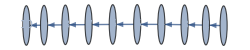

```mathematica
SSSDisplay[sss1b,NetMethod->{NoSSS,GraphPlot},NetSize->250,NetMax->10]
```

```mathematica
SSSDisplay[sss20,NetMethod->{NoSSS,GraphPlot},NetSize->250,NetMax->10]
```

-Graphics-

```mathematica
sss1b["Net"]
sss20["Net"]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20}

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20}

```mathematica
ToNetDifferenceSets@sssF2FF["Net"]
ToReducedNetDifferenceSets@%
```

{{3,4},{1,5,5},{1,1,5},{1,1,5},{5,6},{1,7,7},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,9,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{9,10},{1,11,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{11,12},{1,13,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{13,14},{1,15,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{15,16},{1,17,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{1,1,17},{17,18},{1,19,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{1,1,19},{19,20},{1,21,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{1,1,21},{21,22},{1,23,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1,23},{1,1},{1,1},{1,1},{},{1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
{1·{{1,2}},1·{{1,3,3}},0·{{1,1,3}},
1·{{3,4}},1·{{1,5,5}},2·{{1,1,5}},
1·{{5,6}},1·{{1,7,7}},4·{{1,1,7}},
1·{{7,8}},1·{{1,9,9}},6·{{1,1,9}},
1·{{9,10}},1·{{1,11,11}},8·{{1,1,11}},
1·{{11,12}},1·{{1,13,13}},10·{{1,1,13}},
1·{{13,14}},1·{{1,15,15}},12·{{1,1,15}},
1·{{15,16}},1·{{1,17,17}},14·{{1,1,17}},
1·{{17,18}},1·{{1,19,19}},16·{{1,1,19}},
1·{{19,20}},1·{{1,21,21}},18·{{1,1,21}},
1·{{21,22}},1·{{1,23,23}},17·{{1,1,23}},
3·{{1,1}},1·{{}},1·{{1}},17·{{1,1}}}
```

Constant (2^nd) difference row:  {0·{{2,2}}, 0·{{0,2,2}}, 2·{{0,0,2}}
Zero (3^rd) difference row:	  {0·{{0,0}}, 0·{{0,0,0}}, 0·{{0,0,0}}

#### SummarizeDifferenceSets: Only identifies 1-d cases

```mathematica
SummarizeDifferenceSets::usage = "SummarizeDifferenceSets[L] takes a list of sets of link lengths, as generated by ToNetDifferenceSets[net], and attempts to find a summary.";

SummarizeDifferenceSets[L:List[__List]]:=Module[{k,j,bestk=0, bestj=0},
(* L is a List of zero or more Lists *)
For[k=1, k<Length[L]/2, k++, (* k is substring length, j is offset to previous substring(s) *)
j=2k;(* pass the final subsequence *)
While[(* if still within bounds compare neighboring subsequences *)
(* 
If[j≤Length[L],Print["k = ",k,", j = ",j,", L⟦",-j,";;",-j+k-1,"⟧ = ",L⟦-j;;-j+k-1⟧, ", L⟦",-j+k,";;",-j+2k-1,"⟧ = ",L⟦-j+k;;-j+2k-1⟧,": SubsetQ? ",MapThread[SubsetQ,{L⟦-j;;-j+k-1⟧, L⟦-j+k;;-j+2k-1⟧}]]];
 *)
(j≤Length[L]) && (And@@MapThread[SubsetQ,{L⟦-j;;-j+k-1⟧, L⟦-j+k;;-j+2k-1⟧}]),
If[j>bestj, bestj=j; bestk=k; (* Print["new best {j,k}: ", {bestj,bestk}] *) ]; (* update best *)
j += k;  (* jump to next pair to compare *)
];
If[j>k,j-=k]; (* if possible, backup to the last good match *)
While[(* now advance backwards one at a time: RotateLeft subsequences *)
0<j≤Length[L] && -j+k-1>0 && And@@MapThread[SubsetQ,{L⟦-j;;-j+k-1⟧, L⟦-j+k;;-j+2k-1⟧}],
If[j>bestj, bestj=j; bestk=k; Print["new best {j,k}: ", {bestj,bestk}]]; (* update best *)
j++
]
];
Print@{bestk, bestj};
Print["Summary: ", L⟦-bestj;;-bestj+bestk-1⟧, " : ",Round[bestj/bestk,.1]," reps = ",Round[100*bestj/Length[L],1],"%" ];
Print["Canonical: ", 
Row[{#," ⇔ ",FromNetDifferenceSets[#]}]& @ First[Sort@NestList[RotateLeft,L⟦-bestj;;-bestj+bestk-1⟧, bestk]]];
If[$debug,Print@Column@Partition[L⟦-bestj;;-1⟧,bestk,bestk,1,{}]];
];
```

```mathematica
ToNetDifferenceSets@sss20["Net"]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
SummarizeDifferenceSets@ToNetDifferenceSets@sss20["Net"]
```

{1,19}

Summary: {{1}} : 19. reps = 100%

Canonical: {{1}} ⇔ {1→2}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

```mathematica
SummarizeDifferenceSets@%
```

```mathematica
SummarizeDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

{10,20}

Summary: {{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11}} : 2. reps = 27%

Canonical: {{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11}} ⇔ {1→2,1→2,1→2,2→3,2→3,2→12,3→4,3→4,3→14,4→5,4→5,4→15,5→6,5→6,5→16,6→7,6→7,6→17,7→8,7→8,7→18,8→9,8→9,8→19,9→10,9→10,9→20,10→11,10→11,10→21}

{{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11}}
{{},{1,1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

### Old Code

#### Identification strategies

1.  If $SSSTEvolution stops changing (last 2 elements are equal), the SSS is Dead, as of the first instance of the repetition.  If the SSS is Dead, so is the network.  [Done]

2a.  If any two elements of $SSSEvolution are the same, the SSS is Repeating, and will repeat from then on.  Note:  for efficency, we only test whether the last element is repeated anywhere before.  Since the test happens every step, it will catch the first time it happens, and assign a value to $SSSVerdict, which remains until reinitialized.  If the SSS is Repeating, so is the network.  [Done]

2b.  If Repeating, also look for unused rules (in the repeating part):  possible long-jump.  This is implemented in TestForUnusedRules.  [Not yet in V8, Need to check.]

3.  Having “enough” repetitions in $SSSHistory sets $SSSVerdict to Pseudorepeating, meaning the SSS may be repeating, n-dimensional, or exponential.  Before this happens there’s no point in applying additional tests to the SSS or its network.  [Not implemented in this version.]

Possible strategies:

4.  Old network test (should be reinvoked?):  Take a section of $SSSNet including 500 consecutive nodes, and look for matches elsewhere in $SSSNet.  An identical match gives a high probability of a 1-d network, even though the SSS never repeats.  (Better:  require 5 matches)

5.  If a large segment of $SSSRuleUsage repeats, it is likely that the network is repeating.  Even if exact repetition does not occur, find the positions where the least frequently used rule was used and try to identify the pattern from repeated differences and ratios of differences.  (NOTE:  It is currently unclear whether an exponential fit for this data implies an exponential network.  Look at apparent exponential cases, including NKS 91e, comparing the SSS behavior and the network behavior. Caution:  many exponential networks use the same rule or subset of rules for a long time before a different rule can be applied again.)  To decrease the likelihood of incorrect identification, require that the last 90% of $SSSRuleUsage repeats, including 5 repetitions, and merge intervals before testing.  [Implementing as LeastUsedRulePositions.]

6.  In working with intervals, such as above, always make sure each interval uses the same rules, working backward from the last completed interval:  if a change occurs, adjust or merge intervals.  If n^th interval uses fewer rules than the (n-1)^st, merge the n^th with whatever follows.  If n^th interval uses more rules than the (n-1)^st, merge the (n-1)^st with whatever precedes it.  If the number of prospective intervals falls below 5, abandon attempt.  [Implementing as MergeIntervalsByRulesUsed.]

7.  Look for a pattern in the positions of the commonest element of $SSSHistory.  Since the addition of the tag (4^th part of each element, set to increment or decrement to avoid false positives when pre- or post-match strings are changing length), the commonest element is likely to have a 0 tag, and may follow a simple pattern.  Note:  merge intervals before testing.  [Not implemented in this version, was implemented as CommonestHistoryPositions.]

8.  If after 500 steps the last 90% of $SSSRuleUsage (see #5) all uses the same subset of the ruleset, whether or not the behavior can be identified, if not all rules are used in the the last 90%, it is likely that the SSS (and network) is a duplicate of an earlier case, and can be skipped or can even trigger a long-jump.  This would be highly desirable. [Need to do.]

9.  New network test:  Use $SSSOutDegreeRemaining to decide which is the first node that might have new paths leading off it.  Ideally this would be the first non-zero in the list, but Pseudorepeating (growing) SSSs may repeatedly create some cells that will never be destroyed, corresponding to some nodes that retain a non-zero value in $SSSOutDegreeRemaining, in which case it may be difficult to definitely determine the index. Tally $SSSDistance⟦1;;index⟧ to give the number of nodes (n) a distance (d) from the network origin.  (Any data past this index is probably incomplete, and should be disregarded.)  Try to fit that data to a polynomial or exponential curve and/or identify the pattern from repeated differences and ratios of differences.  [Implemented as DistanceTally.]

Note: Any identifiable pattern in the first half of $SSSOutDegreeRemaining might allow a larger index to be used, indicating a pattern among the nodes that never will be “complete”, in which case distance data could be used up to where the pattern breaks, i.e., where new branches can be expected.  OR: if there are any 1s in the first half of $SSSOutDegreeRemaining, use the position of the first 2 as the index, etc.

10.  For each n, find the last node that is a distance n from the origin, up to the index mentioned in #9.  After merging intervals, seek a pattern in these values.  Caution:  in a directed network this gives different results than in an undirected one, and different from previous tests.  [Implemented as DistanceLastPositions.]

11.  Look for a pattern in the list of positions of maximum-length states in $SSSEvolution (greatest string length seen up to that point).  [Implemented as MaxStateLengthPositions.]

12.  Consider position of match in the state string.  Does a minimum or maximum position (minimum distance from end) keep recurring?  If so, restart at first such position, skipping junk before this point in the evolution and deleting unused stuff at beginning/end of state string.

13.  Consider positions of least-frequent repeated case in last 2/3 of $SSSInDegree and and reliable part of $SSSOutDegree.

```mathematica
CommonestHistoryPositions
checkDimension@MergeIntervals@%
```

#### SSS & Net Tests

Needed functions:

```mathematica
myRatios[l_List,n_Integer?Positive] := 
If[n≥Length[l],{},
ListConvolve[Flatten[{1,Table[0,{n-1}],-1}],l,{-1,1},{},Power[#2,#1]&,Times]
]
```

SSS Tests:

```mathematica
CommonestHistoryPositions := If[MatchQ[$SSSVerdict,""|"Dead"],{},
Flatten@Position[$SSSHistory,First@Commonest[$SSSHistory⟦;;Round[Length[$SSSHistory]/2,1]⟧]]]
```

```mathematica
SSSEvolve[50]
```

1

```mathematica
CommonestHistoryPositions
```

{16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126}

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{1,{16,2},16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 60 | 62 | 64 | 66 | 68 | 70 | 72 | 74 | 76 | 78 | 80 | 82 | 84 | 86 | 88 | 90 | 92 | 94 | 96 | 98 | 100 | 102 | 104 | 106 | 108 | 110 | 112 | 114 | 116 | 118 | 120 | 122 | 124 | 126
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
RiffleDistanceTally := Module[{diffs,rats,identified=False,n,data=Differences[DistanceTally],mx},
Off[Power::infy,Infinity::indet,Power::indet];
mx=Length[data];
n=1;
While[identified===False && n≤mx,
If[MatchQ[diffs=Differences[data,1,n],
{Repeated[_,{0,5}],Repeated[b_,{4,∞}],Repeated[_,{0,3}]}],
identified="2",
If[MatchQ[rats=myRatios[diffs,n],
{Repeated[_,{0,5}],Repeated[b_,{3,∞}],Repeated[_,{0,3}]}],
identified="exp",
n++]
]
];
On[Power::infy,Infinity::indet,Power::indet];
Switch[identified,
False,{"failed"},
"exp",{"exp"," riffling by ",n,": ",rats},
"2",{"2"," riffling by ",n,": ",diffs}
]
]
```

```mathematica
RiffleDistanceTally
```

{2, riffling by ,1,: ,{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Differences[DistanceTally]
```

{1,2,3,5,7,10,13}

```mathematica
Differences[Differences[DistanceTally],1,2]
```

{2,3,4,5,6}

```mathematica
Differences@%
```

{1,1,1,1}

```mathematica
{1,2,5,12,29,65,137,270,503,890,1507,2454,3863,5901,8779,12756}[[1;;-1;;2]]
FindSequenceFunction[%,n]
```

{1,5,29,137,503,1507,3863,8779}

1/180 (-180+534 n-253 n^2+30 n^3+65 n^4-24 n^5+8 n^6)

```mathematica
{1,2,5,12,29,65,137,270,503,890,1507,2454,3863,5901,8779,12756}[[2;;-1;;2]]
FindSequenceFunction[%,n]
```

{2,12,65,270,890,2454,5901,12756}

1/180 (330 n-133 n^2+120 n^3+35 n^4+8 n^6)

```mathematica
Differences[{1,2,5,12,29,65,137,270,503,890,1507,2454,3863,5901,8779,12756},1,2]
Differences@%
Differences@%
Differences@%
Differences@%
Differences@%
```

{4,10,24,53,108,205,366,620,1004,1564,2356,3447,4916,6855}

{6,14,29,55,97,161,254,384,560,792,1091,1469,1939}

{8,15,26,42,64,93,130,176,232,299,378,470}

{7,11,16,22,29,37,46,56,67,79,92}

{4,5,6,7,8,9,10,11,12,13}

{1,1,1,1,1,1,1,1,1}

```mathematica
Differences[{1,2,5,12,29,65,137,270,503,890,1507,2454},1,2]
Differences@%
Differences@%
Differences@%
Differences@%
Differences@%
```

{4,10,24,53,108,205,366,620,1004,1564}

{6,14,29,55,97,161,254,384,560}

{8,15,26,42,64,93,130,176}

{7,11,16,22,29,37,46}

{4,5,6,7,8,9}

{1,1,1,1,1}

#### This shows that I must extend RiffleDistanceTally to do the same sort of multiline operation that checkDimension already does! ####

#### IdentifyPseudorepeating

```mathematica
$debug=False
```

False

```mathematica
IdentifyPseudorepeating := Module[{sssAns,distanceTallyAns,sssSummary,distanceTallySummary},
Which[
$SSSVerdict=="Dead", Return[{}],

10Max[$SSSNet/.Rule->List]<Length[$SSSEvolution],
If[$debug,Print[n,". ",rs," : No network after step ",Max[$SSSNet/.Rule->List],", now at ",Length[$SSSEvolution]]];
Return[{}]
];
sssAns=checkDimension/@MergeIntervals /@ MinRulePositions;
sssAns=Which[
Length[sssAns]==0,{"failed"},
Length[sssAns]== 1,sssAns⟦1⟧,
!(Equivalent@@sssAns⟦All,1⟧),{"failed"},
Equivalent@@sssAns⟦All,1⟧, {sssAns⟦1,1⟧,First[Sort[sssAns⟦All,2;;3⟧]]},
True,{"failed"}
];
sssAns={
sssAns, (* simplified ans from MinRulePositions *)
checkDimension@MergeIntervals@MaxStateLengthPositions,
checkDimension@MergeIntervals@CommonestHistoryPositions,
checkDimension@MergeIntervals@DistanceLastPositions
}; (* combine with results of the other tests *)

If[$debug,Print[sssAns]]; 

sssSummary=Select[sssAns,First[#]≠"failed"&];
If[Length[sssSummary]>0,
sssSummary=sssSummary⟦All,1;;2⟧;
If[!(Equivalent@@(First/@sssSummary)),
If[$debug,Print["SSS tests give different answers: ", sssSummary];Print[sssAns]];sssSummary={}
]
];

If[$debug,Print["sssSummary: ",sssSummary]]; 

distanceTallyAns = {checkDimension@DistanceTally,RiffleDistanceTally};

(*
If[Length[sssSummary]>0 && sssSummary⟦1,1⟧=="1", (* DistanceTally & RiffleDistanceTally catastrophically fail for 1-d *)
distanceTallyAns={{"1","overriding!"}},
distanceTallyAns = {checkDimension@DistanceTally,RiffleDistanceTally}
];  
*)

If[$debug,Print["distanceTallyAns: ",distanceTallyAns]];

distanceTallySummary = Union[Select[First /@ distanceTallyAns,#≠"failed"&]];

If[$debug,Print["distanceTallySummary: ",distanceTallySummary]]; 


If[Length[distanceTallySummary]>0 && distanceTallySummary[[1]]=="1",distanceTallySummary={"1"}];  (* remove this kludge when function is extended, currently RiffleDistanceTally  *)

If[Length[distanceTallySummary]==2,
If[$debug,Print["Error: checkDimension@DistanceTally and RiffleDistanceTally disagree:  "]; Print[distanceTallySummary]];
distanceTallySummary={}
];

Which[
Length[distanceTallySummary]==0, 
If[$debug,Print["Distance tally tests unsuccessful"]]; {False,{sssAns,distanceTallyAns}},

Length[sssSummary]==0,
If[$debug,Print["No successful SSS tests"]];
If[$SSSVerdict=!="Repeating",
{$SSSVerdict,$SSSRepetitionInterval,$SSSRepetitionStart}={distanceTallySummary⟦1⟧,∞,∞}
];
{True,distanceTallySummary⟦1⟧<>"qq"},

Length[sssSummary]==1 && sssSummary⟦1,1⟧== distanceTallySummary⟦1⟧,
If[$debug,Print["Only one successful SSS test"]]; 
If[$SSSVerdict=!="Repeating",{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}=sssSummary⟦1⟧];
{True,sssSummary⟦1⟧/.s_String:>s<>"q"},

Union[First/@sssSummary,distanceTallySummary]≠Union[distanceTallySummary],
If[$debug,Print["CAUTION: SSS tests and distance tally tests disagree: ",{First/@sssSummary,distanceTallySummary}]]; 
If[$SSSVerdict=!="Repeating",
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}=Sort[sssSummary]⟦1⟧;
$SSSVerdict=distanceTallySummary⟦1⟧<>"x"<>Sort[sssSummary]⟦1,1⟧
];
{True,distanceTallySummary⟦1⟧<>"x"<>Sort[sssSummary]⟦1,1⟧,Sort[sssSummary]⟦1,2;;⟧},

True,
If[$SSSVerdict=!="Repeating",
{$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}}=Sort[sssSummary]⟦1⟧
];
{True,Sort[sssSummary]⟦1⟧}
]
];
```

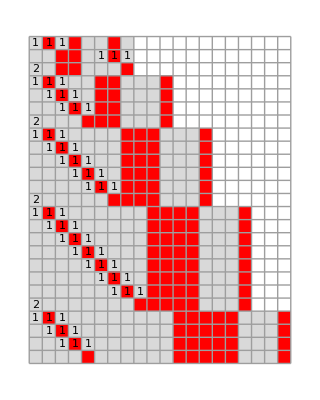


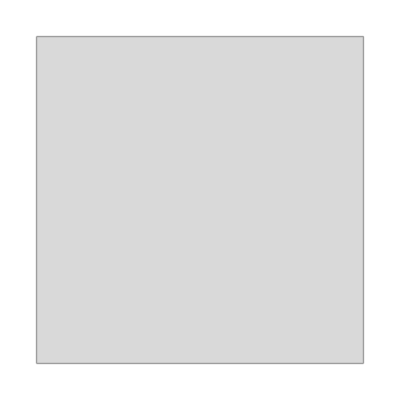
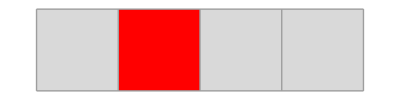
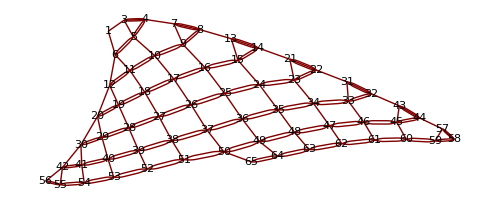
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"ABA"->"AAB","A"->"ABAA"}, "ABABAABA",75,EarlyReturn->True,SSSMax->25,NetMax->65,NetSize->500]
```

```mathematica
SSSEvolve[50]
```

Pseudorepeating

```mathematica
IdentifyPseudorepeating
```

match ({3,3,3,3,-8,-1,-1,-1,-1,-1}) with Partition[data,2], starting at 1

{True,{2,{3,∞}}}

```mathematica
SSSEvolve[10]
IdentifyPseudorepeating
```

2

{{2,{3,∞},3 | 7 | 13 | 21 | 31 | 43 | 57 | 73
4 | 6 | 8 | 10 | 12 | 14 | 16 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{4,∞},4 | 8 | 14 | 22 | 32 | 44 | 58 | 74
4 | 6 | 8 | 10 | 12 | 14 | 16 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{failed,1
,{}},{failed,6 | 12 | 20 | 30 | 42 | 56
6 | 8 | 10 | 12 | 14 | 
2 | 2 | 2 | 2 |  | 
0 | 0 | 0 |  |  | ,{Indeterminate,Indeterminate}}}

sssSummary: {{2,{3,∞}},{2,{4,∞}}}

distanceTallyAns: {{failed,1 | 3 | 7 | 12 | 19 | 27 | 37
2 | 4 | 5 | 7 | 8 | 10 | 
2 | 1 | 2 | 1 | 2 |  | 
-1 | 1 | -1 | 1 |  |  | 
2 | -2 | 2 |  |  |  | ,{-1.,-1.}},{2, riffling by ,2,: ,{3,3,3,3}}}

distanceTallySummary: {2}

{True,{2,{3,∞}}}

```mathematica
SSSEvolve[100]
IdentifyPseudorepeating
```

2

{{2,{3,∞},3 | 7 | 13 | 21 | 31 | 43 | 57 | 73 | 91 | 111 | 133 | 157 | 183
4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{4,∞},4 | 8 | 14 | 22 | 32 | 44 | 58 | 74 | 92 | 112 | 134 | 158 | 184
4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{43,∞},43 | 57 | 73 | 91 | 111 | 133 | 157 | 183
14 | 16 | 18 | 20 | 22 | 24 | 26 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{6,∞},6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132 | 156
6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }}

sssSummary: {{2,{3,∞}},{2,{4,∞}},{2,{43,∞}},{2,{6,∞}}}

match ({3,3,3,3,3}) with Partition[data,2], starting at 1

distanceTallyAns: {{2,{1,∞},1 | 3 | 7 | 12 | 19 | 27 | 37 | 48 | 61 | 75 | 91 | 108
2 | 4 | 5 | 7 | 8 | 10 | 11 | 13 | 14 | 16 | 17 | 
2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 |  | },{2, riffling by ,2,: ,{3,3,3,3,3,3,3,3,3}}}

distanceTallySummary: {2}

{True,{2,{3,∞}}}

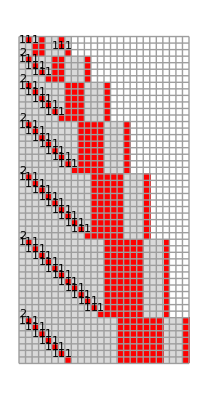
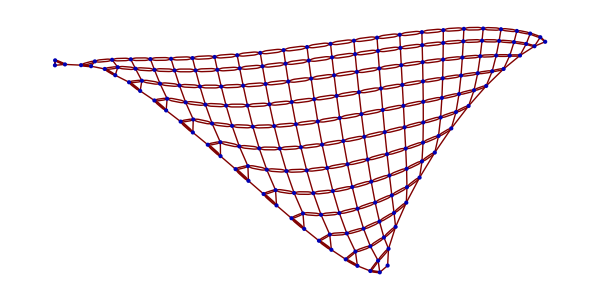
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[SSSMax->50,NetSize->{600,300},VertexLabeling->Tooltip]
```

```mathematica
DistanceTally
```

{1,3,6,10,16,23,31,40,50,61,73,86,100,115,131,148,166,185}

```mathematica
checkDimension@%
```

{dim,2,1 | 3 | 6 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
2 | 3 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
{2,2,2,"failed","failed","failed"}
```